```mathematica
f[z_]:=(z^2+5)/((z-1)(z^2+5));
f[z]//Simplify
```

1/(-1+z)

```mathematica
Solve[Denominator[f[z]//Simplify]==0,z]
```

{{z→1}}

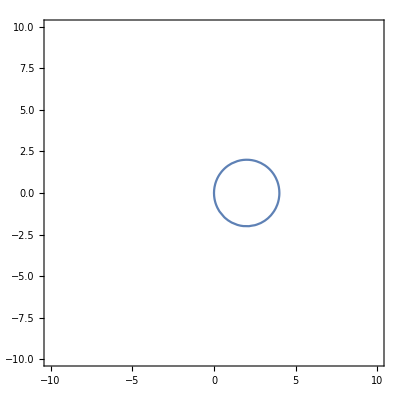

```mathematica
ContourPlot[{Abs[x+I y -2]==2,x+I y ==1},{x,10,-10},{y,10,-10}]
```

```mathematica
c=2
path=Circle[{2,0},2]
result=(1/(2 Pi I)) Integrate[f[z]/(z-c),{z,path}]
```

2

Circle[{2,0},2]

Integrate::ilim: Invalid integration variable or limit(s) in {z,Circle[{2,0},2]}.

-(ⅈ Integrate[1/((-2+z) (-1+z)),{z,Circle[{2,0},2]}])/(2 π)

```mathematica
Exit[]
```